micromotion sideband:

WolframAlphaQueryNoResults

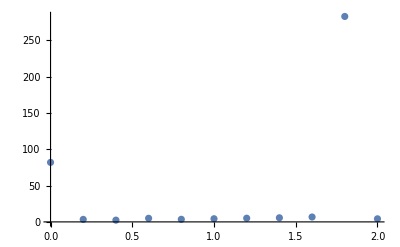

{{0.4,2.43568},{0.8,3.57364},{1.,4.34708},{1.2,5.07225},{1.4,5.67889},{1.6,6.73416}}

FittedModel[3.10578+1.3663 X]

```mathematica
nx={40.74838773,
1.508099697,
1.010419,
2.254997652,
1.567503355,
1.949329938,
2.308555325,
2.609675678,
3.134357052,
141.2871405,
1.907789935
};
y=1/(Sqrt[(nx+1)/nx]-1);
x=Range[0,2,0.2];
data={{x[[1]],y[[1]]}};
Do[data=Append[data,{x[[i]],y[[i]]}],{i,2,Length[x],1}]
ListPlot[data,PlotRange->All]
outliers={data[[1]],data[[-2]]};
nonoutliers=Delete[data,{{1},{-2}}];
dataForfit=Delete[data,{{1},{-2},{2},{4},{-1}}]
lm=LinearModelFit[nonoutliers,X,X]
```

FittedModel[0.875423+3.52956 X]

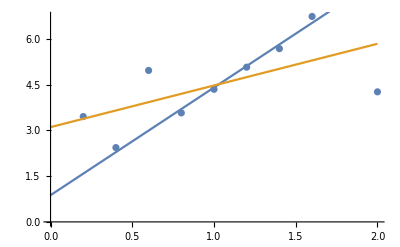

```mathematica
lm1=LinearModelFit[dataForfit,X,X]
Show[ListPlot[nonoutliers],Plot[{lm1[X],lm[X]},{X,0,2}]]
```

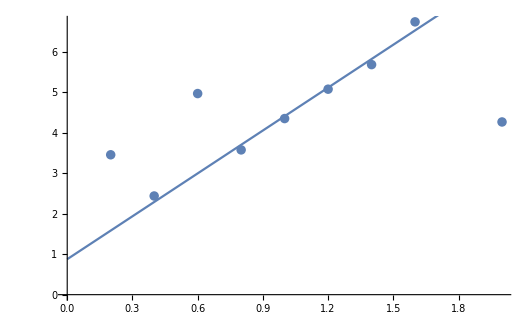

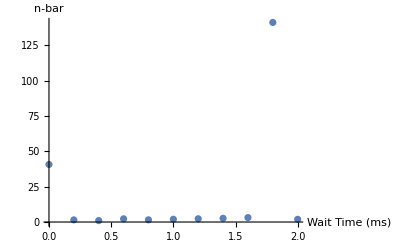

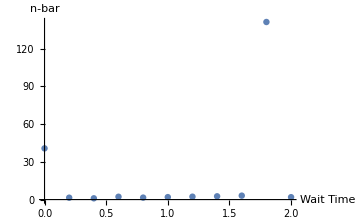

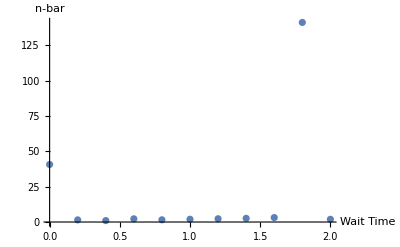

```mathematica
Show[%483,AxesLabel->{None,None},PlotLabel->None,LabelStyle->{14,GrayLevel[0]}]
```